```mathematica
f[x_,y_]:=2 x^2+2 y^2;
```

```mathematica
g[x_,y_]:=(x-2)^2+y^2;
```

```mathematica
ll[x_,y_,z_]:=f[x,y]+l g[x,y]
```

```mathematica
Grad[ll[x,y,l],{x,y,l}]
```

{2 l (-2+x)+4 x,4 y+2 l y,(-2+x)^2+y^2}

```mathematica
Solve[{2 l (-2+x)+4 x==0,4 y+2 l y==0,(-2+x)^2+y^2==0},{x,y,l}]
```

{}

```mathematica
p1=Plot3D[g[x,y],{x,-5,5},{y,-5,5},Axes->True,PlotRange->{-1,5},ClippingStyle->None,PlotStyle->{Orange},AxesOrigin->{0,0,0},Mesh->None,Boxed->False];
```

```mathematica
p2=Plot3D[f[x,y],{x,-5,5},{y,-5,5},Axes->True,PlotRange->{-1,5},ClippingStyle->None,PlotStyle->{Blue},AxesOrigin->{0,0,0},Mesh->None,Boxed->False];
```

```mathematica
Show[p1,p2]
```

-Graphics3D-

```mathematica
L[x_]:=f[x[[1]],x[[2]]]+x[[3]]g[x[[1]],x[[2]]]
```

```mathematica
data=Tuples[Table[i,{i,-1,1,.3}],3];
```

```mathematica
results=Table[{data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],L[data[[i]]]},{i,1,Length[data]}];
```

```mathematica
Graphics3D[{ColorData["DarkRainbow"][#[[4]]],PointSize->Large,Point[#[[1;;3]]]}&/@results]
```

```mathematica
ListContourPlot3D[f[x,y]+l g[x,y],{x,-1,1,.2},{y,-1,1,.2},{l,-1,1,.2},Contours->{0},Mesh->None]
```

ListContourPlot3D::nonopt: Options expected (instead of {l, -1, 1, 0.2}) beyond position 3 in ListContourPlot3D[2\ x^2 + 2\ y^2 + l\ ((-2 + x)^2 + y^2), {x, -1, 1, 0.2}, {y, -1, 1, 0.2}, {l, -1, 1, 0.2}, Contours → {0}, Mesh → None]. An option must be a rule or a list of rules.

ListContourPlot3D[2 x^2+2 y^2+l ((-2+x)^2+y^2),{x,-1,1,0.2},{y,-1,1,0.2},{l,-1,1,0.2},Contours→{0},Mesh→None]

```mathematica
f[x_,y_]:=2 x^2+2 y^2;
```

```mathematica
g[x_,y_]:=(x-2)^2+y^2;
```

```mathematica
p1=Plot3D[g[x,y],{x,-5,5},{y,-5,5},Axes->True,PlotRange->{-1,5},ClippingStyle->None,PlotStyle->{Orange},AxesOrigin->{0,0,0},Mesh->None,Boxed->False];
```

```mathematica
p2=Plot3D[f[x,y],{x,-5,5},{y,-5,5},Axes->True,PlotRange->{-1,5},ClippingStyle->None,PlotStyle->{Blue},AxesOrigin->{0,0,0},Mesh->None,Boxed->False];
```

```mathematica
Show[p1,p2]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot3D[f[x,y]+l g[x,y],{x,-5,5},{y,-5,5},{l,-5,5},AxesOrigin->{0,0,0},Mesh->None,Boxed->False,Contours->{a}],{a,-20,20}]
```

-Graphics3D-

```mathematica
Gamma[a+1]/Gamma[a]
```

```mathematica
Gamma[1+a]/Gamma[a]//FullSimplify
```

a

```mathematica
D[Log[μ^n(x1 x2 x3)^(μ-1)],μ]
```

```mathematica
(x1 x2 x3)^(1-μ) μ^-n (n (x1 x2 x3)^(-1+μ) μ^(-1+n)+(x1 x2 x3)^(-1+μ) μ^n Log[x1 x2 x3])//FullSimplify
```

n/μ+Log[x1 x2 x3]

```mathematica
Log[μ^n(x1 x2 x3)^(μ-1)]//FullSimplify
```

Log[(x1 x2 x3)^(-1+μ) μ^n]

```mathematica
-(n+m)/(lx+ly)+n/lx//FullSimplify
```

```mathematica
n/lx-(m+n)/(lx+ly)//Together
```

(-lx m+ly n)/(lx (lx+ly))

```mathematica
m/ly-(m+n)/(lx+ly)//Together
```

(lx m-ly n)/(ly (lx+ly))

```mathematica
n/(Log[x1]+Log[x2]+Log[x3])-(m+n)/(Log[x1]+Log[x2]+Log[x3]+Log[y1]+Log[y2]+Log[y3])//Together
```

(-m Log[x1]-m Log[x2]-m Log[x3]+n Log[y1]+n Log[y2]+n Log[y3])/((Log[x1]+Log[x2]+Log[x3]) (Log[x1]+Log[x2]+Log[x3]+Log[y1]+Log[y2]+Log[y3]))

```mathematica
x^Log[x]
```

```mathematica
x^Log[x]//FullSimplify
```

x^Log[x]

```mathematica
x^(1/Log[x])//FullSimplify
```

ⅇ

```mathematica
Log[x,x]/Log[x,ⅇ]//FullSimplify
```

Log[x]

```mathematica
Log[x,x]
```

1

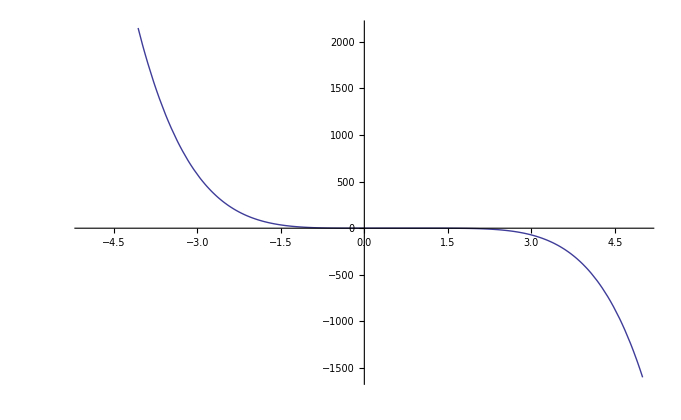

```mathematica
Plot[T^2(1-T)^3,{T,-5,5}]
```

```mathematica
D[t^n(1-t)^m,{t,2}]//FullSimplify
```

```mathematica
(1-t)^(-2+m) t^(-2+n) ((-1+n) n-2 n (-1+m+n) t+(-1+m+n) (m+n) t^2)/.t->n/(m+n)
```

```mathematica
(n/(m+n))^(-2+n) (1-n/(m+n))^(-2+m) ((-1+n) n-(n^2 (-1+m+n))/(m+n))//FullSimplify
```

```mathematica
-(m^2 (m/(m+n))^(-3+m) (n/(m+n))^n)/n//Apart
```

-((m/(m+n))^m (n/(m+n))^n (m+n)^3)/(m n)

```mathematica
Solve[-(1-t)^(-1+m) t^(-1+n) (n (-1+t)+m t)==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→1-0^(1/m)},{t→n/(m+n)}}

```mathematica
{{t->1-0^(1/m)},{t->at at}}
```

```mathematica
Plot[x^2-y^2,{x,-5,5},{y,-5,5},Axes->True,PlotRange->{-1,5},ClippingStyle->None,PlotStyle->{Orange},AxesOrigin->{0,0,0}]
```

Plot::nonopt: Options expected (instead of {y, -5, 5}) beyond position 3 in Plot[x^2 - y^2, {x, -5, 5}, {y, -5, 5}, Axes → True, PlotRange → {-1, 5}, ClippingStyle → None, PlotStyle → {Orange}, AxesOrigin → {0, 0, 0}]. An option must be a rule or a list of rules.

Plot[x^2-y^2,{x,-5,5},{y,-5,5},Axes→True,PlotRange→{-1,5},ClippingStyle→None,PlotStyle→{Orange},AxesOrigin→{0,0,0}]

```mathematica
Plot3D[x^2-y^2,{x,-5,5},{y,-5,5},Axes->False,PlotRange->{-1,5},ClippingStyle->None,PlotStyle->{Blue},AxesOrigin->{0,0,0},Mesh->None,Boxed->True,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
∫_x1^(x x1) (t^2 nu^(n t))/(x1^((n-1)t+1)xj^(t+1))ⅆxj
```

ConditionalExpression[nu^(n t) t x1^(-1+t-n t) (x1^-t-(x x1)^-t),Re[x1]≥0&&(Im[x1]/Im[x1 (-1+Re[x])+x Re[x1]]≤-1||(Re[x1 Im[x]+x Im[x1]]≥Im[x1]&&(Im[x1]≥0||Abs[x1]^2 Im[x]≥0))||(Re[x1 Im[x]+x Im[x1]]≤Im[x1]&&(Im[x1]≤0||Abs[x1]^2 Im[x]≤0)))&&(1/(-1+x)∉Reals||Re[1/(-1+x)]≥0||Re[1/(-1+x)]<-1)]

```mathematica
∫_nu^∞ nu^(n t) t x1^(-1+t-n t) (x1^-t-(x x1)^-t)ⅆx1
```

ConditionalExpression[(1-x^-t)/n,Re[n t]>0&&Re[nu]>0&&Im[nu]==0]

```mathematica
D[(1-x^-t)/n,x]
```

(t x^(-1-t))/n

```mathematica
PDF[PoissonDistribution[1],x]
```

Piecewise[{{1/(ⅇ x!), x≥0}, {0, True}}]

```mathematica
a=Table[1/(ⅇ x!)//N,{x,0,10}]
```

{0.367879,0.367879,0.18394,0.0613132,0.0153283,0.00306566,0.000510944,0.000072992,9.12399×10^-6,1.01378×10^-6,1.01378×10^-7}

```mathematica
Table[Total[a[[i;;Length[a]]]],{i,1,11}]
```

{1.,0.632121,0.264241,0.0803014,0.0189881,0.00365984,0.000594175,0.0000832311,0.0000102391,1.11515×10^-6,1.01378×10^-7}

```mathematica
Length[a]
```

```mathematica
Table[Sum[1/(ⅇ x!),{x,i,10}],{i,0,10}]//N
```

{1.,0.632121,0.264241,0.0803014,0.0189881,0.00365984,0.000594175,0.0000832311,0.0000102391,1.11515×10^-6,1.01378×10^-7}

```mathematica
1.1151548315933272*^-6
```

1.11515×10^-6

```mathematica
.000000111515
```

1.11515×10^-7

```mathematica
Table[Sum[Binomial[5,x] t^x(1-t)^(5-x),{x,i,5}],{i,0,5}]
```

```mathematica
{(1-t)^5+5 (1-t)^4 t+10 (1-t)^3 t^2+10 (1-t)^2 t^3+5 (1-t) t^4+t^5,5 (1-t)^4 t+10 (1-t)^3 t^2+10 (1-t)^2 t^3+5 (1-t) t^4+t^5,10 (1-t)^3 t^2+10 (1-t)^2 t^3+5 (1-t) t^4+t^5,10 (1-t)^2 t^3+5 (1-t) t^4+t^5,5 (1-t) t^4+t^5,t^5}/.t->.5
```

{1.,0.96875,0.8125,0.5,0.1875,0.03125}

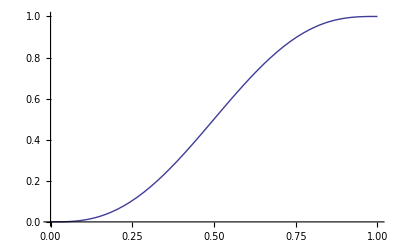

```mathematica
Plot[10 (1-t)^2 t^3+5 (1-t) t^4+t^5,{t,0,1}]
```

```mathematica
(1-t)^5+5 (1-t)^4 t+10 (1-t)^3 t^2+10 (1-t)^2 t^3+5 (1-t) t^4+t^5/.t->.5//N
```

1.

```mathematica
Plot3D
```